```mathematica
CountryData["UnitedStates", "LifeExpectancy"]
```

78.9 yr

```mathematica
data = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData[All]}], {_, _Missing}];
```

```mathematica
Short[data]
```

{{Afghanistan,65.173 yr},{Albania,78.686 yr},{Algeria,77.063 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,61.487 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,77.146 yr},{Argentina,76.813 yr},{Armenia,75.224 yr},{Aruba,76.434 yr},{Australia,83.586 yr},{Austria,81.671 yr},{Azerbaijan,73.123 yr},{Bahamas,74.053 yr},{Bahrain,77.419 yr},«202»,{United Arab Emirates,78.12 yr},{United Kingdom,81.426 yr},{United States,78.9 yr},{United States Virgin Islands,80.747 yr},{Uruguay,78.056 yr},{Uzbekistan,71.848 yr},{Vanuatu,70.623 yr},{Venezuela,72.066 yr},{Vietnam,75.493 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,70.505 yr},{Yemen,66.181 yr},{Zambia,64.194 yr},{Zimbabwe,61.738 yr}}

```mathematica
{{Entity["Country","Afghanistan"].14mathe,Quantity[65.173, "Years"]},«231»,{Entity["Country",""…""],Quantity[61.738, "Years"]}}
```

```mathematica
Short[SortBy[data, Last]]
```

{{Central African Republic,53.679 yr},{Chad,54.505 yr},{Lesotho,54.836 yr},{Nigeria,55.018 yr},{Sierra Leone,55.066 yr},{Somalia,57.697 yr},{South Sudan,58.095 yr},{Ivory Coast,58.104 yr},{Guinea-Bissau,58.634 yr},{Equatorial Guinea,59.057 yr},{Cameroon,59.626 yr},{Mali,59.692 yr},{Eswatini,60.721 yr},{Democratic Republic of the Congo,60.971 yr},{Togo,61.34 yr},{Mozambique,61.387 yr},«202»,{Andorra,82.9 yr},{Sweden,82.946 yr},{Israel,83.123 yr},{Iceland,83.138 yr},{South Korea,83.193 yr},{San Marino,83.4 yr},{Australia,83.586 yr},{Italy,83.663 yr},{Spain,83.693 yr},{Singapore,83.767 yr},{Switzerland,83.921 yr},{Macau,84.37 yr},{Japan,84.766 yr},{Hong Kong,85.003 yr},{Monaco,89.4 yr}}

```mathematica
Short[data]
```

{{Afghanistan,65.173 yr},{Albania,78.686 yr},{Algeria,77.063 yr},{American Samoa,73.9 yr},{Andorra,82.9 yr},{Angola,61.487 yr},{Anguilla,81.6 yr},{Antigua and Barbuda,77.146 yr},{Argentina,76.813 yr},{Armenia,75.224 yr},{Aruba,76.434 yr},{Australia,83.586 yr},{Austria,81.671 yr},{Azerbaijan,73.123 yr},{Bahamas,74.053 yr},{Bahrain,77.419 yr},«202»,{United Arab Emirates,78.12 yr},{United Kingdom,81.426 yr},{United States,78.9 yr},{United States Virgin Islands,80.747 yr},{Uruguay,78.056 yr},{Uzbekistan,71.848 yr},{Vanuatu,70.623 yr},{Venezuela,72.066 yr},{Vietnam,75.493 yr},{Wallis and Futuna Islands,80. yr},{West Bank,75.4 yr},{Western Sahara,70.505 yr},{Yemen,66.181 yr},{Zambia,64.194 yr},{Zimbabwe,61.738 yr}}

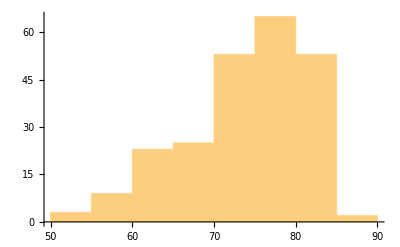

```mathematica
Histogram[data⟦All, 2⟧]
```

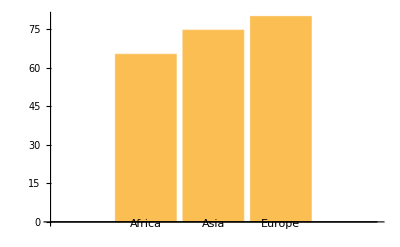

```mathematica
dataAfrica = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Africa"]}], {_, _Missing}];

dataAsia = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Asia"]}], {_, _Missing}];

dataEurope = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["Europe"]}], {_, _Missing}];
BarChart[{
Mean[dataAfrica⟦All, 2⟧],
Mean[dataAsia⟦All, 2⟧],
Mean[dataEurope⟦All, 2⟧]}, ChartLabels->{"Africa", "Asia", "Europe"}]
```

```mathematica
dataSouthAmerica = DeleteCases[
Table[{i, CountryData[i, "LifeExpectancy"]}, {i, CountryData["SouthAmerica"]}], {_, _Missing}];
Take[dataSouthAmerica, 3]
```

{{Argentina,76.813 yr},{Bolivia,71.771 yr},{Brazil,76.084 yr}}

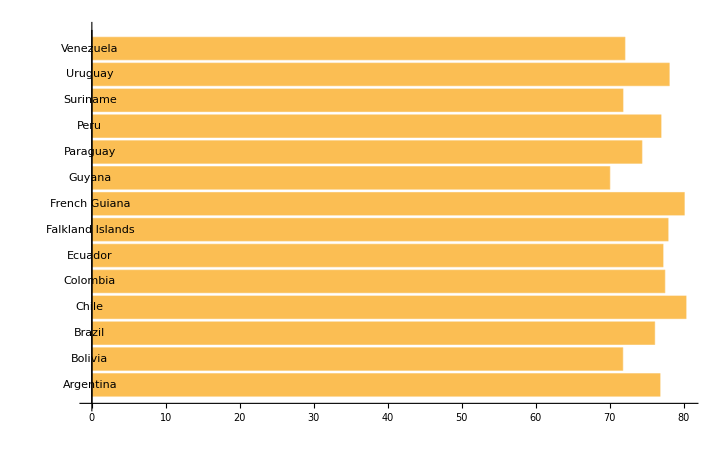

```mathematica
BarChart[dataSouthAmerica⟦All, 2⟧, ChartLabels -> dataSouthAmerica⟦All, 1⟧, BarOrigin -> Left]
```

```mathematica
?Tooltip
```

```mathematica
Tooltip[x + y, "label"]
```

x+y

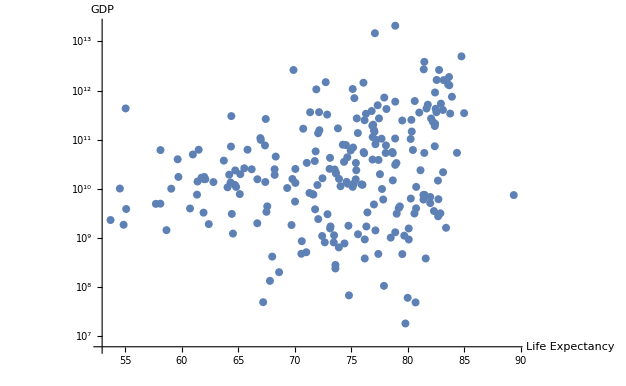

```mathematica
data2 = Table[Tooltip[{CountryData[i, "LifeExpectancy"], CountryData[i, "GDP"]},
CountryData[i, "Name"]], {i, CountryData[]}];
ListLogPlot[data2, AxesLabel->{"Life Expectancy", "GDP"}]
```

```mathematica
Manipulate[
plotFn[Table[Tooltip[{CountryData[i, "LifeExpectancy"],CountryData[i, prop]},
CountryData[i, "Name"]], {i, CountryData[All]}], 
AxesLabel -> {"LifeExpectancy", prop}],
{prop, {"InfantMortalityFraction", "GDP", "LiteracyFraction"}},
{{plotFn, ListLogLogPlot}, {ListPlot, ListLogPlot, ListLogLogPlot}},
SaveDefinitions->True]
```